```mathematica
(***  GIG_GNIG is a Mathematica Notebook which has modules to be used in the computation of the GIG and GNIG pdf's and cdf's and GIG quantiles.
The user functions are:
GIGpdf, GIGcdf, QuantGIG, GNIGpdf and GNIGcdf,
on which help may be obtained by typing ?GIGpdf, ?GIGcdf, ?QuantGIG, ?GNIGpdf and ?GNIGcdf
***)

(***  GIG  ***)

Rat[x_]:=Module[{nn},
If [ToString[Head[x]]≠"Real",x,
nn=StringLength[ToString[x,InputForm]]-1;Round[x*10^nn]/10^nn]]

SetAttributes[Rat,Listable]

Makec[r_,l_,p_]:=Module[{c},
c=Table[Table[1,{j,1,Max[r]}],{i,1,p}];
Do[c[[i,r[[i]]]]=Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,1,i-1}]*Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,i+1,p}]/(r[[i]]-1)!,{i,1,p}];
Do[Do[c[[i,r[[i]]-k]]=Sum[((r[[i]]-k+j-1)!*(Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,1,i-1}]+Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,i+1,p}])*c[[i]][[r[[i]]-(k-j)]])/(r[[i]]-k-1)!,{j,1,k}]/k,{k,1,r[[i]]-1}],{i,1,p}];
c]

GIGpdf[r_,li_,zi_,prec_:150]:=Module[{p,l,c,z},
If[Count[r,_Integer]==Length[r]&&And@@NonNegative[r]&&And@@Positive[li]&&Length[r]==Length[li],
If[zi>0,
p=Length[r];l=Rat[li];c=Makec[r,l,p];z=Rat[zi];
SetPrecision[Product[l[[j]]^r[[j]],{j,1,p}]*Sum[Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec],If[zi==0,0,Print["Third argument must be a non-negative value"]]]]]

GIGpdf::usage="GIGpdf[r, l, z, prec] gives the value for the pdf of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l', computed at the point 'z', with precision 'prec' - he first 3 arguments are mandatory and the 4th one has default value 150";

GIGcdf[r_,li_,zi_,prec_:150]:=Module[{p,l,c,z},
If[Count[r,_Integer]==Length[r]&&And@@NonNegative[r]&&And@@Positive[li]&&Length[r]==Length[li],
If[zi>0,
p=Length[r];l=Rat[li];c=Makec[r,l,p];z=Rat[zi];
1-Product[l[[j]]^r[[j]],{j,1,p}]*SetPrecision[Sum[Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec],If[zi==0,0,Print["Third argument must be a non-negative value"]]]]]

GIGcdf::usage="GIGcdf[r, l, z, prec] gives the value for the cdf of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l', computed at the point 'z', with precision 'prec' - the first 3 arguments are mandatory and the 4th one has default value 150";

QuantGIG[r_,l_,qquant_,eps_:10^-11,pp_:11,ind_:0,xoo_:1,preco_:50]:=Module[{quant,xo,prec,vec,p,ll,c,pr,xa,xb,res,nx,F,F1,F2},
quant=Rat[qquant];
If[TrueQ[xoo==1||xoo==Null],xo=1,xo=Rat[xoo]];
prec=preco;
p=Length[r];
ll=Rat[l];
c=Makec[r,ll,p];
pr=Product[ll[[j]]^r[[j]],{j,1,p}];
F[x_]=GIGcdfsimpfast[r,ll,x,p,pr,c];
While[Length[RealDigits[res=SetPrecision[F[xo],prec]][[1]]]<25*pp,prec=3*prec];
If[res>quant,xa=xo;xo=xo/2;While[SetPrecision[F[xo],prec]>quant,xa=xo;xo=xo/2],
xa=xo;xo=xo*2;While[SetPrecision[F[xo],prec]<quant,xa=xo;xo=xo*2]];
If[xo>xa,xb=xo,xb=xa;xa=xo];
xo=(xa+xb)/2;
res=SetPrecision[F[xo],prec];
While[Abs[res-quant]>Min[10^-3,quant/10],xo=(xa+xb)/2;
If[(res=SetPrecision[F[xo],prec])>quant,xb=xo,xa=xo]];
nx=Rat[xo];
xa=0;
If[ind==0||ind==Null,{F1[x_]=GIGpdfsimpfast[r,ll,x,p,pr,c];
While[Abs[nx-xa]>eps,{xa=nx;
nx=xa+(quant-SetPrecision[F[xa],prec])/SetPrecision[F1[xa],prec]}]},
{F1[x_]=GIGpdfsimp[r,ll,x,p,pr,c,prec];
F2[x_]=GIGcdfsimp[r,ll,x,p,pr,c,prec];
While[Abs[nx-xa]>eps,{xa=nx;nx=xa+(quant-F2[Rat[xa]])/F1[Rat[xa]]}]}];SetPrecision[nx,Max[pp,-Log[10,eps]]]]

QuantGIG::usage="QuantGIG[r, l, q, eps, pp, ind, xo, prec] gives the value for the quantile 'q' of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l' - only the first 3 arguments are mandatory ['eps' is the value for the largest difference between consecutive iteration values for the approximate quantile (has a default value of 10^-11); 'pp' is the number of digits for printing the quantile value (has a default value of 11, and anyway the number of digits used to print the quantile is always the maximum between this value and -Log10 of 'eps'); 'ind' is an index which has a default value of zero and if set to a different value will make the module to take an even more precise path of computation for initial values; 'xo' is an initial vlaue for the search of the quantile (it has default value 1 and usually there is no need to change this value since the module is strudy enough to be able to search for good initial values); 'prec' is the number of digits used for the intermediate computations in the module (it has default value of 50)]";

GIGpdfsimp[r_,l_,zi_,p_,pr_,c_,prec_:50]:=Module[{z},
z=Rat[zi];
SetPrecision[pr*Sum[Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec]]

GIGcdfsimp[r_,l_,zi_,p_,pr_,c_,prec_:50]:=Module[{z},
z=Rat[zi];
1-pr*SetPrecision[Sum[Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec]]

GIGpdfsimpfast[r_,l_,z_,p_,pr_,c_,prec_:50]:=
pr*Sum[Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}]

GIGcdfsimpfast[r_,l_,z_,p_,pr_,c_,prec_:50]:=
1-pr*Sum[Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}]



(***  GNIG   ***)

Hgeo[b_,k_,x_]:=Module[{F11,F12,F21,F22,F31,F32,res,gg,gg2,rr},
F11=1;
F12=0;
F21=0;
F22=b;
res=Table[0,{j,1,k}];
rr=Re[(-x)^(-b)*(Gamma[b]-Gamma[b,-x])];
res[[1]]=b*rr;
Do[
{F31=(b+j)/(x*j)*((x+b+j-1)*F21-(b+j-1)*F11);
F32=(b+j)/(x*j)*((x+b+j-1)*F22-(b+j-1)*F12);
F11=F21;
F12=F22;
F21=F31;
F22=F32;
res[[j+1]]=F31*Exp[x]+F32*rr},{j,1,k-1}];
res
]

GNIGpdf[r_,bb_,l_,aa_,ww_,prec_:150] := Module[{g,P,a,b,ll,c,w},
 If[Count[r,_Integer]==Length[r] && And@@NonNegative[r] && And@@Positive[l],
If[ww>0,
g = Length[r];
w=Rat[ww];
ll=Rat[l];
a=Rat[aa];
b=Rat[bb];
c =Makec[r,ll,g];
resn=SetPrecision[Table[Hgeo[b,r[[j]],-(a-ll[[j]])*w],{j,1,g}],prec];
SetPrecision[Product[ll[[j]]^r[[j]], {j, 1, g}]*a^b*Sum[Exp[-ll[[j]]*w]*Sum[c[[j]][[k]]*
         Gamma[k]/Gamma[k+b]*w^(k+b-1)*resn[[j,k]],
         {k,1,r[[j]]}],{j, 1, g}],prec],If[ww==0,0,Print["The running value has to be a non-negative value"]]]
 ] ]

GNIGpdf::usage="GNIGpdf[r, ro, l, lo, z, prec] gives the value for the pdf of a GNIG distribution with a set of integer shape parameters 'r' and non-integer shape parameter 'ro', and rate parameters 'l', corresponding to the integer shape parameters, and shape parameter 'lo', corresponding to the non-integer shape parameter, computed at the point 'z', with precision 'prec' - the first 5 arguments are mandatory and the 6th one has default value 150";

GNIGcdf[r_,bb_,l_,aa_,ww_,prec_:150] := Module[{g,P,a,b,ll,c,w},
If[Count[r,_Integer]==Length[r] && And@@NonNegative[r] && And@@Positive[l],
If[ww>0,
g = Length[r];
w=Rat[ww];
ll=Rat[l];
a=Rat[aa];
b=Rat[bb];
c = Makec[r,ll,g];
resn=SetPrecision[Table[Hgeo[b,r[[j]],-(a-ll[[j]])*w],{j,1,g}],prec];
SetPrecision[a^b*w^b/Gamma[b+1]*Hypergeometric1F1[b,b+1,-a w]-Product[ll[[j]]^r[[j]], {j, 1, g}]*a^b*Sum[Exp[-ll[[j]]*w]*Sum[c[[j]][[k]]/ll[[j]]^k*(k-1)!*
    Sum[w^(b+i)*ll[[j]]^i/Gamma[b+1+i]*
         resn[[j,i+1]],{i,0,k-1}],{k,1,r[[j]]}],
         {j, 1, g}],prec],If[ww==0,0,Print["The running value has to be a non-negative value"]]]
 ] ]

GNIGcdf::usage="GNIGpdf[r, ro, l, lo, z, prec] gives the value for the cdf of a GNIG distribution with a set of integer shape parameters 'r' and non-integer shape parameter 'ro', and rate parameters 'l', corresponding to the integer shape parameters, and shape parameter 'lo', corresponding to the non-integer shape parameter, computed at the point 'z', with precision 'prec' - the first 5 arguments are mandatory and the 6th one has default value 150";
```

0.527422344055815448625388281749716578564372891

0.5320775417247881923817217899287538258035498615

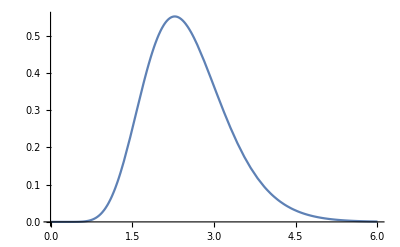

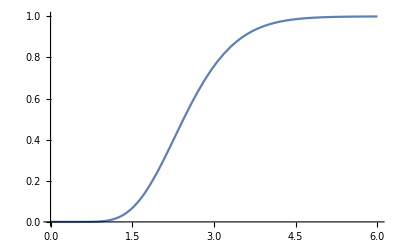

```mathematica
r={3,4,5};
ll={3.4,7.6,4.5};
z=2.5;
GIGpdf[r,ll,z]
GIGcdf[r,ll,z]
Plot[GIGpdf[r,ll,x],{x,0,6}]
Plot[GIGcdf[r,ll,x],{x,0,6}]
```

0.39533820769315890253326935528157147094733440000052

0.18101317358215007971409478633216072788746345269409

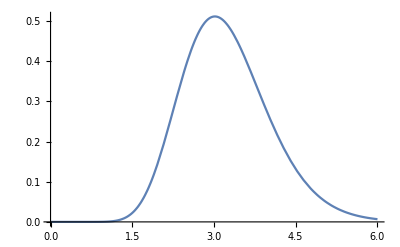

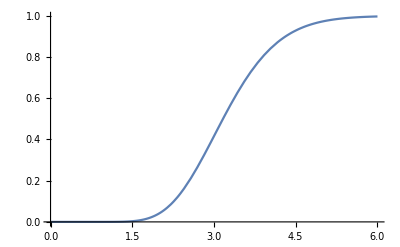

```mathematica
r={3,4,5};
r2=6.4;
ll={3.4,7.6,4.5};
ll2=8.9;
z=2.5;
GNIGpdf[r,r2,ll,ll2,z]
GNIGcdf[r,r2,ll,ll2,z]
Plot[GNIGpdf[r,r2,ll,ll2,x],{x,0,6}]
Plot[GNIGcdf[r,r2,ll,ll2,x],{x,0,6}]
```

```mathematica
r={2,3,4,7,3};
l={2.3,3.4,4.5,6.7,8.9};
QuantGIG[r,l,.95]
QuantGIG[r,l,.95,10^-16]
QuantGIG[r,l,.95,10^-16,20]
```

5.8395809619

5.839580961856236

5.8395809618562364828

```mathematica
r={12,12,14,14,14,14,11,11,11,11,11,13,13,13,13,13,13,13,11,11,11,15,15,14};
ll={12.3,13.3,23.4,24.4,25.4,26.4,6.4,7.4,8.4,9.4,10.4,62.3,63.3,64.3,65.3,66.3,67.3,68.3,27.4,28.4,29.4,74.9,75.9,76.9};
QuantGIG[r,ll,.05,10^-16]
```

12.30539557563194

```mathematica
GIGcdf[r,ll,12.30539557563194347435684981357628195866`16.]
```

0.050000000000000000000000000000000000224693341171814257569285988689566009558907374937537833371712521249934616278

```mathematica
QuantGIG[r,ll,.95,10^-16]
```

15.84316638559754

```mathematica
GIGcdf[r,ll,15.84316638559753521182850426840934222622`16.]
```

0.9499999999999999999999999945791887202776752234369908813903984959485388213451126592286599673986404382890117873489305368676222

```mathematica
GIGcdf[r,ll,QuantGIG[r,ll,.05]]
GIGcdf[r,ll,QuantGIG[r,ll,.95]]
```

0.049999999999999999999999995767968532500006032180646139060192234652555065976444648565681599752962039802160660489

0.9499999999999999999999999945791887202776752234369908813903984959485388213451126592286599673986404382890117873489305368676222

```mathematica
GIGcdf[r,ll,QuantGIG[r,ll,.05,10^-16]]
GIGcdf[r,ll,QuantGIG[r,ll,.95,10^-16]]
```

0.050000000000000000000000000000000000224377154598878476731650777263571782558449449305450779645544108790472093382

0.9499999999999999999999999945791887202776752234369908813903984959485388213451126592286599673986404382890117873489305368676222

```mathematica
GIGcdf[r,ll,QuantGIG[r,ll,.05,10^-30]]
GIGcdf[r,ll,QuantGIG[r,ll,.95,10^-30]]
```

0.050000000000000000000000000000000000000000000647502857903940774170153542762089585742294829196076588893102807013

0.9500000000000000000000000000000000000000579018624374182990711467368164589823775627249678581700010334386433934852528855430688

```mathematica
?QuantGIG
```

QuantGIG[r, l, q, eps, pp, ind, xo, prec] gives the value for the quantile 'q' of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l' - only the first 3 arguments are mandatory ['eps' is the value for the largest difference between consecutive iteration values for the approximate quantile (has a default value of 10^-11); 'pp' is the number of digits for printing the quantile value (has a default value of 11, and anyway the number of digits used to print the quantile is always the maximum between this value and -Log10 of 'eps'); 'ind' is an index which has a default value of zero and if set to a different value will make the module to take an even more precise path of computation for initial values; 'xo' is an initial vlaue for the search of the quantile (it has default value 1 and usually there is no need to change this value since the module is strudy enough to be able to search for good initial values); 'prec' is the number of digits used for the intermediate computations in the module (it has default value of 50)]